```mathematica
theoList={{1.67, 0.074},{8,0.36},{13,0.624},{16.7, 1.0}}
```

{{1.67,0.074},{8,0.36},{13,0.624},{16.7,1.}}

```mathematica
experimentalList={{1.67, 78/1000},{16.7, 893/1000}}
```

{{1.67,39/500},{16.7,893/1000}}

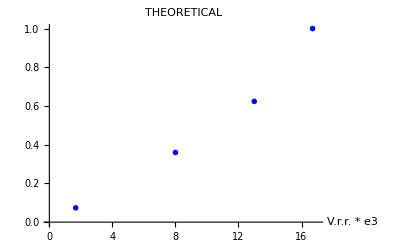

```mathematica
PlotTheoretical=ListPlot[theoList, 
PlotStyle->Blue,
PlotMarkers->{{●,10}},PlotRange->{{0,17},{0,1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"THEORETICAL"]
```

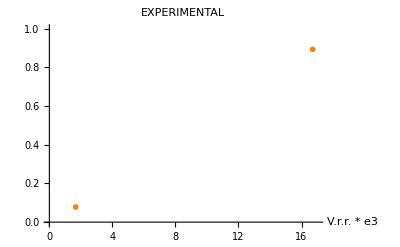

```mathematica
PlotExperimental=ListPlot[experimentalList, 
PlotStyle->Orange,
PlotMarkers->{{●,10}},PlotRange->{{0,17},{0,1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"EXPERIMENTAL"]
```

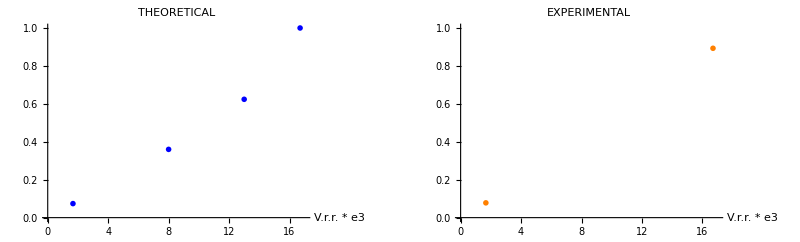

```mathematica
GraphicsRow[{PlotTheoretical, PlotExperimental}]
```

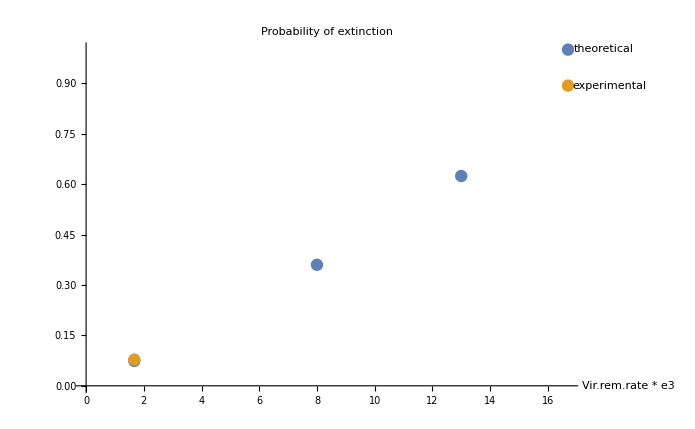

```mathematica
ListPlot[{Labeled[theoList,"theoretical"],Labeled[experimentalList,"experimental"]},AxesLabel->{"Vir.rem.rate * e3",""},PlotLabel->"Probability of extinction"]
```